## Figure 1

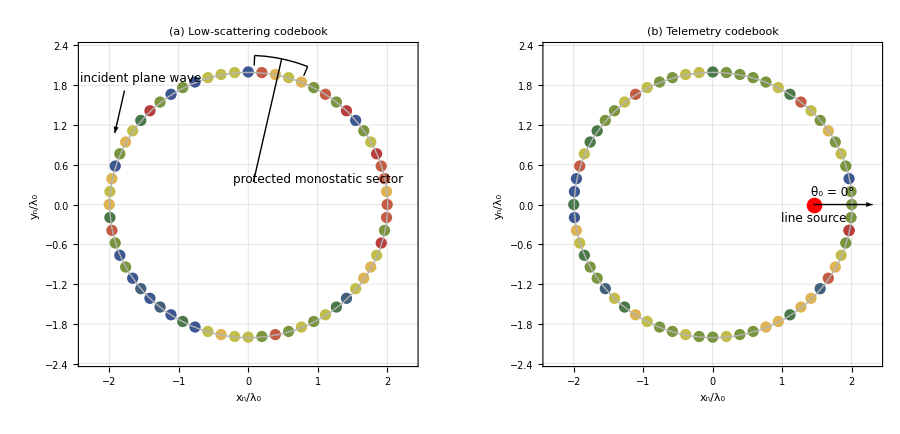

C:\Users\mrkho_000\Desktop\2026_TAP_Ghala\figures\Clean_Figs\fig1_configuration_reformatted.pdf

```mathematica
(* ==================================================================== *)
  (* FIGURE 1 AND CSVs: GEOMETRY, SHARED STATES, AND TWO CONTROL WORDS     *)
  (* ==================================================================== *)
fig1Data={{2,0,7,4},{1.9903694533443939,0.1960342806591212,6,4},{1.9615705608064609,0.3901806440322565,7,1},{1.9138806714644176,0.5805693545089247,7,4},{1.8477590650225735,0.7653668647301796,8,5},{1.76384252869671,0.9427934736519953,5,4},{1.6629392246050905,1.1111404660392044,4,6},{1.546020906725474,1.268786568327291,1,4},{1.4142135623730951,1.4142135623730951,8,5},{1.268786568327291,1.546020906725474,4,7},{1.1111404660392044,1.6629392246050905,7,3},{0.9427934736519953,1.76384252869671,4,5},{0.7653668647301796,1.8477590650225735,6,4},{0.5805693545089247,1.9138806714644176,5,4},{0.3901806440322565,1.9615705608064609,6,4},{0.1960342806591212,1.9903694533443939,7,4},{0,2,1,3},{-0.196034280659121,1.9903694533443939,5,5},{-0.390180644032256,1.9615705608064609,5,5},{-0.580569354508924,1.9138806714644176,5,4},{-0.765366864730179,1.8477590650225735,1,4},{-0.942793473651995,1.76384252869671,4,5},{-1.1111404660392,1.6629392246050905,1,7},{-1.26878656832729,1.546020906725474,4,5},{-1.41421356237309,1.4142135623730951,8,4},{-1.54602090672547,1.268786568327291,3,4},{-1.66293922460509,1.1111404660392044,5,3},{-1.76384252869671,0.9427934736519953,6,3},{-1.84775906502257,0.7653668647301796,4,5},{-1.91388067146441,0.5805693545089247,1,7},{-1.96157056080646,0.3901806440322565,6,1},{-1.99036945334439,0.1960342806591212,5,1},{-2,0,6,3},{-1.99036945334439,-0.196034280659121,3,1},{-1.96157056080646,-0.390180644032256,7,6},{-1.91388067146441,-0.580569354508924,4,5},{-1.84775906502257,-0.765366864730179,1,3},{-1.76384252869671,-0.942793473651995,4,4},{-1.66293922460509,-1.1111404660392,1,4},{-1.54602090672547,-1.26878656832729,2,2},{-1.41421356237309,-1.41421356237309,1,5},{-1.26878656832729,-1.54602090672547,2,3},{-1.1111404660392,-1.66293922460509,1,6},{-0.942793473651995,-1.76384252869671,3,5},{-0.765366864730179,-1.84775906502257,1,4},{-0.580569354508924,-1.91388067146441,5,4},{-0.390180644032256,-1.96157056080646,6,5},{-0.196034280659121,-1.99036945334439,5,4},{0,-2,5,4},{0.1960342806591212,-1.99036945334439,4,5},{0.3901806440322565,-1.96157056080646,7,4},{0.5805693545089247,-1.91388067146441,4,4},{0.7653668647301796,-1.84775906502257,5,6},{0.9427934736519953,-1.76384252869671,4,6},{1.1111404660392044,-1.66293922460509,5,3},{1.268786568327291,-1.54602090672547,3,6},{1.4142135623730951,-1.41421356237309,2,6},{1.546020906725474,-1.26878656832729,5,2},{1.6629392246050905,-1.1111404660392,6,7},{1.76384252869671,-0.942793473651995,6,6},{1.8477590650225735,-0.765366864730179,5,5},{1.9138806714644176,-0.580569354508924,8,4},{1.9615705608064609,-0.390180644032256,4,8},{1.9903694533443939,-0.196034280659121,7,4}};

coords=N[fig1Data[[All,{1,2}]]];
qS=Round[fig1Data[[All,3]]];
qT=Round[fig1Data[[All,4]]];

Clear[codebookPlot];
(* ================================================================*)
(*EDITABLE FORMATTING PARAMETERS*)
(* ================================================================*) 
titleFont=12;
frameLabelFont=12;
tickFont=10;
annotationFont=12;
smallAnnotationFont=12;
pointSize=0.018;
panelSize=450;
colors=Table[ColorData["DarkRainbow"][N[(k-1)/7]],{k,8}];
(*Examples of individual color changes:*)
(*colors[[1]]=Red;*)
(*colors[[4]]=RGBColor[0.15,0.45,0.85];*)

(* ================================================================*)
(*GENERAL CODEBOOK-PLOTTING FUNCTION*)
(* ================================================================*) codebookPlot[coords_List,q_List,colors_List,label_String,annotations_List]:=Show[ListPlot[Table[Pick[coords,q,k],{k,Length[colors]}],PlotStyle->Table[Directive[colors[[k]],PointSize[pointSize]],{k,Length[colors]}],AspectRatio->1,Frame->True,PlotRange->{{-2.35,2.35},{-2.35,2.35}},FrameLabel->{Style["x_n/λ_0",frameLabelFont,FontFamily->"Times"],Style["y_n/λ_0",frameLabelFont,FontFamily->"Times"]},PlotLabel->Style[label,titleFont,FontFamily->"Times"],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.88]],BaseStyle->{FontFamily->"Times",tickFont}],Graphics[Join[{{GrayLevel[0.7],Thin,Circle[{0,0},2.]}},annotations]],ImageSize->panelSize];

(*** constructing an angular wedge ***)
Clear[sectorOnShaft];
sectorOnShaft[thetaCenter_,halfWidth_,rStart_: 0.35,rInner_:2.1,rOuter_: 2.25]:=Module[{u},u[theta_]:={Cos[theta],Sin[theta]};
{(*Central shaft extending beyond the cylinder*) 
{Black,Thick,Line[{rStart u[thetaCenter],rOuter u[thetaCenter]}]},
(*Exterior angular wedge*) {Black,Thick,Line[{rInner u[thetaCenter-halfWidth],rOuter u[thetaCenter-halfWidth]}],Circle[{0,0},rOuter,{thetaCenter-halfWidth,thetaCenter+halfWidth}],Line[{rOuter u[thetaCenter+halfWidth],rInner u[thetaCenter+halfWidth]}]}}];

(********* Panel (a): low Scattering ***********************)lowScatteringAnnotations={{Black,Thick,Arrow[{{-1.78,1.72},{-1.92,1.08}}]},Text[Style["incident plane wave",annotationFont,FontFamily->"Times"],{-1.55,1.92}],sectorOnShaft[77.65  Degree,10 Degree],Text[Style["protected monostatic sector",smallAnnotationFont,FontFamily->"Times"],{1,0.4}]};

(*********** Panel (b): telemetry *********************)
telemetryAnnotations={{Red,PointSize[0.025],Point[{1.45,0.}]},{Black,Thick,Arrow[{{1.45,0.},{2.3,0.}}]},Text[Style["θ_0 = 0°",annotationFont,FontFamily->"Times"],{1.73,0.2}],Text[Style["line source",smallAnnotationFont,FontFamily->"Times"],{1.45,-0.2}]};

p11=codebookPlot[coords,qS,colors,"(a) Low-scattering codebook",lowScatteringAnnotations];
p12=codebookPlot[coords,qT,colors,"(b) Telemetry codebook",telemetryAnnotations];
fig1=GraphicsGrid[{{p11,p12}},ImageSize->900,Spacings->30];

(**** Combine and Display ***)
fig1 

(***** Export *****)
Export[FileNameJoin[{NotebookDirectory[],"fig1_configuration_reformatted.pdf"}],fig1]
```

## Figure 2

The initialization cell below is needed to generate the remaining figures 2 - 6

```mathematica
(*Folder containing the Figure 2-5 CSV files.*) 
mainDir=NotebookDirectory[];
(*Use this only if the Fourier-Galerkin CSV has also been copied into the notebook folder.*) 
fgDir=mainDir;
(*--------------------CSV utilities--------------------*) 
readCSV[dir_String,file_String]:=Module[{path,raw},path=FileNameJoin[{dir,file}];
If[FileType[path]=!=File,Print["ERROR: file not found: ",path];
Return[$Failed];];
raw=Quiet[Check[Import[path,"CSV"],$Failed]];
If[raw===$Failed||!ListQ[raw]||Length[raw]<2,Print["ERROR: could not read CSV file: ",path];
Return[$Failed];];
Rest[raw]];
numericPairs[data_List,x_Integer,y_Integer]:=Module[{rows},rows=Select[data,ListQ[#]&&Length[#]≥Max[x,y]&&NumberQ[#[[x]]]&&NumberQ[#[[y]]]&];
If[rows==={},{},N[rows[[All,{x,y}]]]]];
(*--------------------Common formatting--------------------*) 
titleFont=12;
frameLabelFont=12;
tickFont=10;
legendFont=12;
polarTickFont=9;
polarAngleFont=10;
fullFigureSize=900;
blueCurve=RGBColor[0.000,0.447,0.741];
orangeCurve=RGBColor[0.850,0.325,0.098];
greenCurve=RGBColor[0.466,0.674,0.188];
grayCurve=GrayLevel[0.35];
baseStyle={FontFamily->"Times",FontSize->legendFont};
axisLabel[x_]:=Style[x,FontFamily->"Times",FontSize->frameLabelFont];
plotTitle[x_]:=Style[x,FontFamily->"Times",FontSize->titleFont];
legendLabels[labels_List]:=(Style[#,FontFamily->"Times",FontSize->legendFont]&/@labels);
```

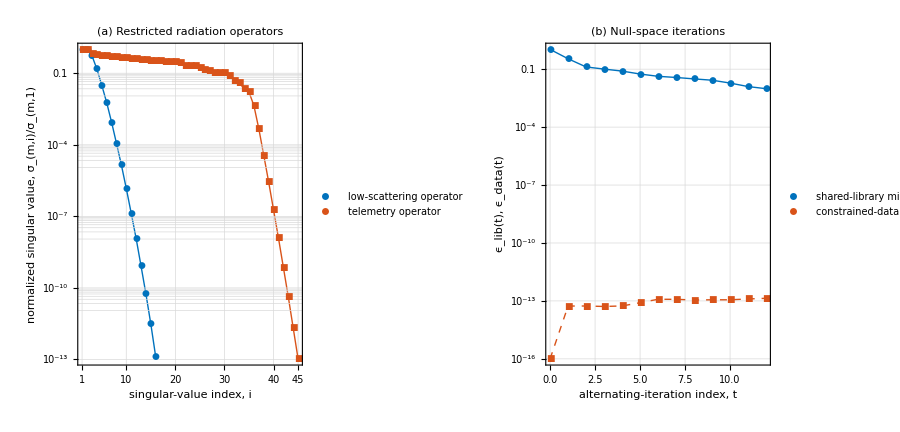

```mathematica
(* ==================================================================== *)
  (* FIGURE 2 AND CSVs: INVERSE SPECTRA AND CORRECTED ITERATION HISTORY    *)
  (* ==================================================================== *)

(******** Panel 2a *********)

d2a=readCSV[mainDir,"fig2a_inverse_normalized_singular_spectra.csv"];
lowSpectrum=numericPairs[d2a,1,2];
telemetrySpectrum=numericPairs[d2a,1,3];
(*Convert the stored zero-based indices to the recommended one-based singular-value index i.*)lowSpectrum[[All,1]]=lowSpectrum[[All,1]]+1;
telemetrySpectrum[[All,1]]=telemetrySpectrum[[All,1]]+1;
p2a=ListLogPlot[{lowSpectrum,telemetrySpectrum},Joined->True,PlotMarkers->Automatic,Frame->True,PlotRange->{{1,45},All},PlotRangePadding->{{0,0},Automatic},FrameTicks->{{Automatic,None},{{{1,"1"},{10,"10"},{20,"20"},{30,"30"},{40,"40"},{45,"45"}},None}},FrameLabel->{axisLabel[Row[{"singular-value index, ",Style["i",Italic]}]],axisLabel[Row[{"normalized singular value, ",Subscript[σ,"m,i"],"/",Subscript[σ,"m,1"]}]]},PlotLabel->plotTitle["(a) Restricted radiation operators"],PlotStyle->{{blueCurve,Thick},{orangeCurve,Thick}},PlotLegends->Placed[legendLabels[{"low-scattering operator","telemetry operator"}],{0.6,0.32}],GridLines->Automatic,BaseStyle->baseStyle];

(******** Panel 2b *********)

d2b=readCSV[mainDir,"fig2b_inverse_iteration_history.csv"];
libraryMismatch=d2b[[All,{1,2}]];
dataChange=d2b[[All,{1,3}]];
(*Logarithmic axes cannot display the exact zero at t=0. The CSV remains unchanged;only the plotted copy is floored.*)dataChange[[All,2]]=(Max[#,10^-16]&)/@dataChange[[All,2]];
p2b=ListLogPlot[{libraryMismatch,dataChange},Joined->True,PlotMarkers->Automatic,Frame->True,PlotRange->{{0,12},All},PlotRangePadding->{{0,0},Automatic},FrameLabel->{axisLabel[Row[{"alternating-iteration index, ",Style["t",Italic]}]],axisLabel[Row[{Subscript[ϵ,"lib"],"(t),  ",Subscript[ϵ,"data"],"(t)"}]]},PlotLabel->plotTitle["(b) Null-space iterations"],PlotStyle->{{blueCurve,Thick},{orangeCurve,Dashed,Thick}},PlotLegends->Placed[legendLabels[{"shared-library mismatch","constrained-data change"}],{0.67,0.44}],GridLines->Automatic,BaseStyle->baseStyle];

(***** Combine and display *******)
fig2=GraphicsGrid[{{p2a,p2b}},ImageSize->fullFigureSize,Spacings->30];

(**** Combine and Display *****)
fig2

(************* Export ****************)
Export[FileNameJoin[{NotebookDirectory[],"fig2_inverse_reformatted.pdf"}],fig2];
```

## Figure 3

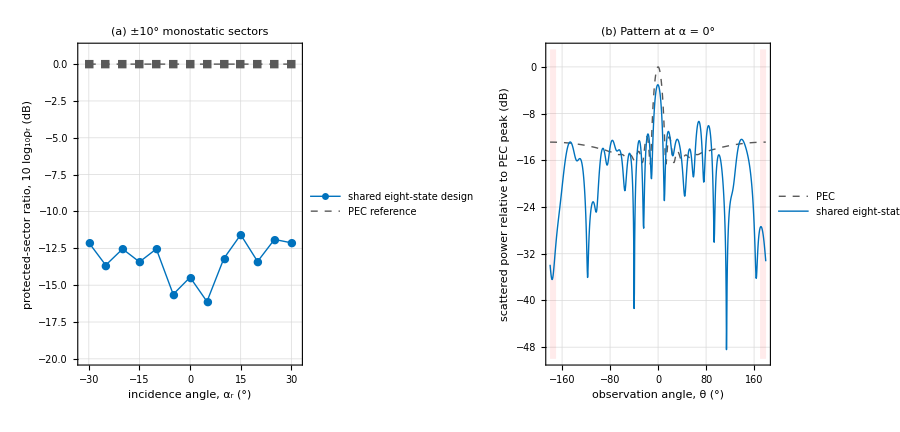

```mathematica
(* ==================================================================== *)
  (* FIGURE 3 AND CSVs: INCIDENCE SWEEP AND NORMAL-INCIDENCE PATTERN       *)
  (* ==================================================================== *)
  

(**********Panel 3a**********)

d3a=readCSV[mainDir,"fig3a_incidence_sweep.csv"];
protectedSectorCurve=d3a[[All,{1,3}]];
pecReference=Transpose[{d3a[[All,1]],ConstantArray[0.,Length[d3a]]}];
p3a=ListLinePlot[{protectedSectorCurve,pecReference},Joined->True,PlotMarkers->{Automatic,None},Frame->True,PlotRange->{{-32,32},{-20,1}},FrameLabel->{axisLabel[Row[{"incidence angle, ",Subscript[α,r]," (°)"}]],axisLabel[Row[{"protected-sector ratio, 10 ",Subscript["log",10],Subscript[ρ,r]," (dB)"}]]},PlotLabel->plotTitle["(a) ±10° monostatic sectors"],PlotStyle->{{blueCurve,Thick},{grayCurve,Dashed,Thick}},PlotLegends->Placed[legendLabels[{"shared eight-state design","PEC reference"}],{0.7,0.55}],GridLines->Automatic,BaseStyle->baseStyle];

(**************Panel 3b******************)

d3b=readCSV[mainDir,"fig3b_normal_incidence_scattering_pattern.csv"];
pecPattern=d3b[[All,{1,2}]];
sharedPattern=d3b[[All,{1,3}]];
p3b=ListLinePlot[{pecPattern,sharedPattern},Joined->True,Frame->True,PlotRange->{{-180,180},{-50,3}},FrameLabel->{axisLabel[Row[{"observation angle, ",θ," (°)"}]],axisLabel["scattered power relative to PEC peak (dB)"]},PlotLabel->plotTitle[Row[{"(b) Pattern at ",α," = 0°"}]],PlotStyle->{{grayCurve,Dashed,Thick},{blueCurve,Thick}},PlotLegends->Placed[legendLabels[{"PEC","shared eight-state design"}],{0.6,0.16}],(*Wrapped protected sector for alpha=0 deg.*)Prolog->{Directive[Red,Opacity[0.08]],Rectangle[{-180,-50},{-170,3}],Rectangle[{170,-50},{180,3}]},GridLines->Automatic,BaseStyle->baseStyle];
fig3=GraphicsGrid[{{p3a,p3b}},ImageSize->fullFigureSize,Spacings->30];

 (***** Combine and display *******) 
fig3

(************* Export ****************)
Export[FileNameJoin[{NotebookDirectory[],"fig3_scattering_reformatted.pdf"}],fig3];
```

## Figure 4

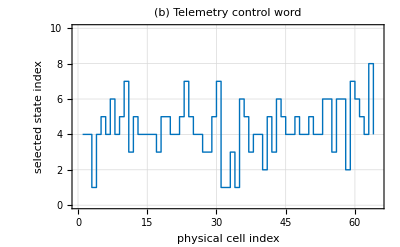

```mathematica
(* ==================================================================== *)
  (* FIGURE 4 AND CSVs: POLAR TELEMETRY PATTERN AND 64-CELL CONTROL WORD  *)
  (* ==================================================================== *)
  

(************Polar plot helper fucntion*************)Clear[polarCartesian,polarGridLines,polarGridLabels,stepCoordinatesXY];
polarCartesian[data_List]:=Module[{xy},xy=({#[[2]] Cos[#[[1]]],#[[2]] Sin[#[[1]]]}&)/@data;
Append[xy,First[xy]]];
polarGridLines[maxRadius_,radialTicks_List]:=Join[{Directive[GrayLevel[0.82],Thin]},(Circle[{0,0},#[[1]]]&)/@Select[radialTicks,#[[1]]>0&],(Line[{{0,0},maxRadius {Cos[#],Sin[#]}}]&)/@(Range[0,7] Pi/4)];
polarGridLabels[maxRadius_,radialTicks_List]:=Join[(Text[Style[#[[2]],polarTickFont,FontFamily->"Times"],{#[[1]],0},{-1.15,-1.15}]&)/@radialTicks,{Text[Style["0°",polarAngleFont,FontFamily->"Times"],{1.1 maxRadius,0}],Text[Style["90°",polarAngleFont,FontFamily->"Times"],{0,1.1 maxRadius}],Text[Style["180°",polarAngleFont,FontFamily->"Times"],{-1.1 maxRadius,0}],Text[Style["-90°",polarAngleFont,FontFamily->"Times"],{0,-1.1 maxRadius}]}];
stepCoordinatesXY[x_List,y_List]:=Join[Flatten[Table[{{x[[k]],y[[k]]},{x[[k+1]],y[[k]]}},{k,1,Length[x]-1}],1],{{Last[x],Last[y]}}];

(*****************Panel 4a*****************)

d4a=readCSV[mainDir,"fig4a_telemetry_polar_pattern.csv"];
telemetryAngles=d4a[[All,1]] Degree;
telemetryDB=d4a[[All,3]];
freeSpaceDB=d4a[[All,4]];
radialMaximum=35.;
radialMinimumDB=-35.;
telemetryPolarData=Transpose[{telemetryAngles,radialMaximum+(Max[radialMinimumDB,#]&/@telemetryDB)}];
freeSpacePolarData=Transpose[{telemetryAngles,radialMaximum+(Max[radialMinimumDB,#]&/@freeSpaceDB)}];
p4a=ListLinePlot[{polarCartesian[telemetryPolarData],polarCartesian[freeSpacePolarData]},Joined->True,PlotRange->{{-40,40},{-40,40}},PlotRangePadding->None,AspectRatio->1,PlotRangeClipping->False,ImagePadding->{{18,18},{6,10}},ImageSize->290,Axes->False,Frame->False,Prolog->polarGridLines[radialMaximum,{{5,"-30"},{15,"-20"},{25,"-10"},{35,"0"}}],Epilog->polarGridLabels[radialMaximum,{{5,"-30"},{15,"-20"},{25,"-10"},{35,"0"}}],PlotStyle->{{blueCurve,Thick},{grayCurve,Dashed,Thick}},PlotLabel->plotTitle["(a) Normalized telemetry pattern"],PlotLegends->Placed[LineLegend[{Directive[blueCurve,Thick],Directive[grayCurve,Dashed,Thick]},legendLabels[{"shared eight-state design","free-space line source"}],LegendLayout->"Column"],Below],BaseStyle->baseStyle];

(****************Panel 4b**********)

d4b=readCSV[mainDir,"fig4b_telemetry_control_word.csv"];
cellIndices=Round[d4b[[All,1]]];
telemetryStateIndices=Round[d4b[[All,3]]];
controlWordData=stepCoordinatesXY[cellIndices,telemetryStateIndices];
p4b=ListLinePlot[controlWordData,Frame->True,PlotRange->{{0,65},{0,10}},FrameLabel->{axisLabel["physical cell index"],axisLabel["selected state index"]},PlotLabel->plotTitle["(b) Telemetry control word"],PlotStyle->{blueCurve,Thick},GridLines->Automatic,BaseStyle->baseStyle];
fig4=GraphicsGrid[{{p4a,p4b}},ImageSize->{fullFigureSize,400},Spacings->0];

(***** Combine and display *******)
fig4

(************* Export ****************)
Export[FileNameJoin[{NotebookDirectory[],"fig4_telemetry_reformatted.pdf"}],fig4];
```

## Figure 5

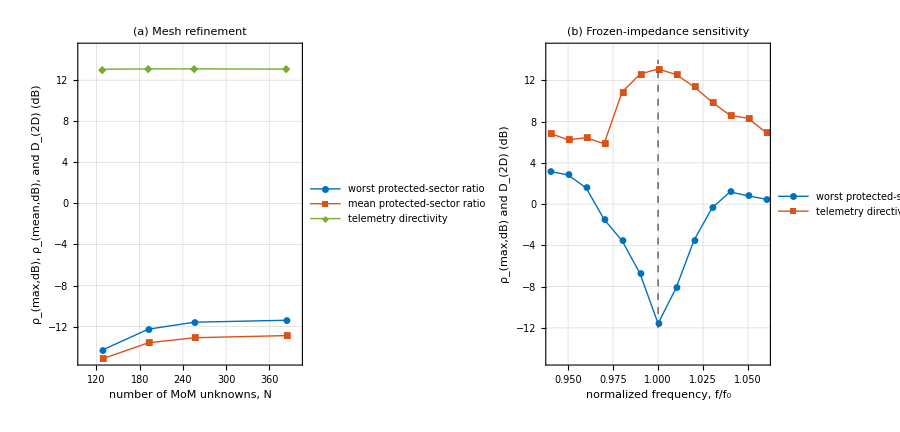

```mathematica
(* ==================================================================== *)
  (* FIGURE 5 AND CSVs: MESH CONVERGENCE AND FREQUENCY SENSITIVITY        *)
  (* ==================================================================== *)
  
(*********Panel 5a***********)

d5a=readCSV[mainDir,"fig5a_mesh_convergence.csv"];
meshWorstRatio=d5a[[All,{1,2}]];
meshMeanRatio=d5a[[All,{1,3}]];
meshDirectivity=d5a[[All,{1,5}]];
p5a=ListLinePlot[{meshWorstRatio,meshMeanRatio,meshDirectivity},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{axisLabel["number of MoM unknowns, N"],axisLabel[Row[{Subscript[ρ,"max,dB"],", ",Subscript[ρ,"mean,dB"],", and ",Subscript["D","2D"]," (dB)"}]]},PlotRange->{{100,400},{Automatic,15}},PlotLabel->plotTitle["(a) Mesh refinement"],PlotStyle->{{blueCurve,Thick},{orangeCurve,Thick},{greenCurve,Thick}},PlotLegends->Placed[legendLabels[{"worst protected-sector ratio","mean protected-sector ratio","telemetry directivity"}],{0.75,0.65}],GridLines->Automatic,BaseStyle->baseStyle];

(**********Panel 5b**************)

d5b=readCSV[mainDir,"fig5b_frozen_impedance_frequency_sweep.csv"];
frequencyWorstRatio=d5b[[All,{1,2}]];
frequencyDirectivity=d5b[[All,{1,4}]];
p5b=ListLinePlot[{frequencyWorstRatio,frequencyDirectivity},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{axisLabel[Row[{"normalized frequency, ",Style["f",Italic],"/",Subscript[Style["f",Italic],0]}]],axisLabel[Row[{Subscript[ρ,"max,dB"]," and ",Subscript["D","2D"]," (dB)"}]]},PlotRange->{Automatic,{-15,15}},PlotLabel->plotTitle["(b) Frozen-impedance sensitivity"],PlotStyle->{{blueCurve,Thick},{orangeCurve,Thick}},PlotLegends->Placed[legendLabels[{"worst protected-sector ratio","telemetry directivity"}],{0.55,0.5}],(*Design-frequency marker.*)Epilog->{grayCurve,Dashed,Thick,Line[{{1.,-12},{1.,14}}]},GridLines->Automatic,BaseStyle->baseStyle];
fig5=GraphicsGrid[{{p5a,p5b}},ImageSize->fullFigureSize,Spacings->30];

(***** Combine and display *******)
fig5
(************* Export ****************)
Export[FileNameJoin[{NotebookDirectory[],"fig5_validation_reformatted.pdf"}],fig5];
```

## Figure 6

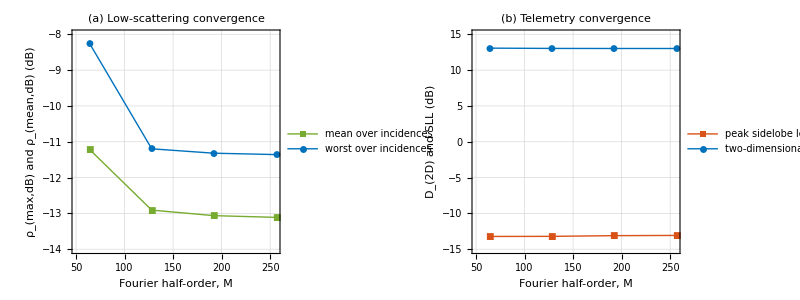

```mathematica
d6=readCSV[fgDir,"fig6_fg_validation_convergence.csv"];

(**********Panel 6a*********)
fgWorstRatio=d6[[All,{1,3}]];
fgMeanRatio=d6[[All,{1,4}]];
p6a=ListLinePlot[{fgWorstRatio,fgMeanRatio},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{axisLabel[Row[{"Fourier half-order, ",Style["M",Italic]}]],axisLabel[Row[{Subscript[ρ,"max,dB"]," and ",Subscript[ρ,"mean,dB"]," (dB)"}]]},ImageSize->450,PlotLabel->plotTitle["(a) Low-scattering convergence"],PlotStyle->{{blueCurve,Thick},{greenCurve,Thick}},PlotRange->{{50,Automatic},{-14,-8}},PlotLegends->Placed[LineLegend[{Directive[blueCurve,Thick],Directive[greenCurve,Thick]},legendLabels[{"worst over incidences","mean over incidences"}],LegendLayout->"ReversedColumn"],{{0.75,0.75},{0.6,0.6}}],GridLines->Automatic,BaseStyle->baseStyle];


(********Panel 6b*********)
fgDirectivity=d6[[All,{1,7}]];
fgSidelobeLevel=d6[[All,{1,8}]];
p6b=ListLinePlot[{fgDirectivity,fgSidelobeLevel},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{axisLabel[Row[{"Fourier half-order, ",Style["M",Italic]}]],axisLabel[Row[{Subscript["D","2D"]," and SLL (dB)"}]]},ImageSize->450,PlotLabel->plotTitle["(b) Telemetry convergence"],PlotStyle->{{blueCurve,Thick},{orangeCurve,Thick}},PlotRange->{{50,Automatic},{-15,15}},PlotLegends->Placed[LineLegend[{Directive[blueCurve,Thick],Directive[orangeCurve,Thick]},legendLabels[{"two-dimensional directivity","peak sidelobe level"}],LegendLayout->"ReversedColumn"],{{0.62,0.62},{0.6,0.6}}],GridLines->Automatic,BaseStyle->baseStyle];
fig6=Grid[{{p6a,p6b}},Alignment->{Center,Top},Spacings->4];

(***** Combine and display *******)
fig6

(************* Export ****************)
Export[FileNameJoin[{NotebookDirectory[],"fig6_FourierGalerkin_reformatted.pdf"}],fig6];
```